Worksheet #2
Problem 6a

```mathematica
k = {{2,1,0},{1,2,1},{0,1,2}};
```

```mathematica
k//MatrixForm
```

(2 | 1 | 0
1 | 2 | 1
0 | 1 | 2)

```mathematica
Solve[Thread[k.{x,y,z}=={0,1,0}],{x,y,z}]
```

{{x→-1/2,y→1,z→-1/2}}

```mathematica
Inverse[k].{0,1,0}
```

{-1/2,1,-1/2}

Problem 6b

```mathematica
Integrate[Exp[-x](a+b x + c x^2),{x,0,1}]
```

a+b+2 c-(a+2 b+5 c)/ⅇ

```mathematica
Integrate[(u+v x + w x^2)(a+b x + c x^2),{x,0,1}]
```

a u+(b u)/2+(c u)/3+(a v)/2+(b v)/3+(c v)/4+(a w)/3+(b w)/4+(c w)/5

```mathematica
Coefficient[a+b+2 c-(a+2 b+5 c)/ⅇ,a,1]==Coefficient[a u+(b u)/2+(c u)/3+(a v)/2+(b v)/3+(c v)/4+(a w)/3+(b w)/4+(c w)/5,a,1]
```

1-1/ⅇ==u+v/2+w/3

```mathematica
Coefficient[a+b+2 c-(a+2 b+5 c)/ⅇ,b,1]==Coefficient[a u+(b u)/2+(c u)/3+(a v)/2+(b v)/3+(c v)/4+(a w)/3+(b w)/4+(c w)/5,b,1]
```

1-2/ⅇ==u/2+v/3+w/4

```mathematica
Coefficient[a+b+2 c-(a+2 b+5 c)/ⅇ,c,1]==Coefficient[a u+(b u)/2+(c u)/3+(a v)/2+(b v)/3+(c v)/4+(a w)/3+(b w)/4+(c w)/5,c,1]
```

2-5/ⅇ==u/3+v/4+w/5

```mathematica
Solve[{1-1/ⅇ==u+v/2+w/3,1-2/ⅇ==u/2+v/3+w/4,2-5/ⅇ==u/3+v/4+w/5},{u,v,w}]
```

{{u→(3 (-29+11 ⅇ))/ⅇ,v→-(12 (-46+17 ⅇ))/ⅇ,w→(30 (-19+7 ⅇ))/ⅇ}}

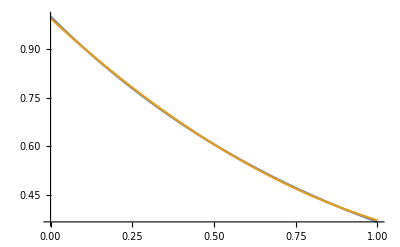

```mathematica
Plot[{Exp[-x],(u+v x + w x^2)/.{u->(3 (-29+11 ⅇ))/ⅇ,v->-(12 (-46+17 ⅇ))/ⅇ,w->(30 (-19+7 ⅇ))/ⅇ}},{x,0,1}]
```

Problem 7

```mathematica
Integrate[x x^(i-1)D[x D[x^(j-1),x],x],{x,0,1},Assumptions->{i>=1, j>=1}]
```

(-1+j)^2/(-1+i+j)

```mathematica
Integrate[x x^(m-1)x^(j-1),{x,0,1},Assumptions->{m>=1,j>=1}]
```

1/(j+m)

The line below constructs a 2D array of equations, then flattens this into a 1D array (i.e. a list) of equations, then solves the system of equations

```mathematica
Solve[Flatten[Table[(j-1)^2/(i+j-1)==Sum[Subscript[a, m ,i]/(m+j),{m,1,3}],{i,1,3},{j,1,3}]],Flatten[Table[Subscript[a, i,j],{i,1,3},{j,1,3}]]]
```

{{a_(1,1)→120,a_(1,2)→100,a_(1,3)→84,a_(2,1)→-510,a_(2,2)→-420,a_(2,3)→-351,a_(3,1)→440,a_(3,2)→360,a_(3,3)→300}}